{x→-0.0948936}

{x→0.104615}

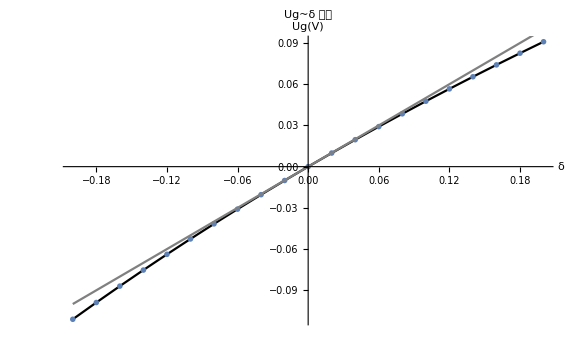

```mathematica
(* Exp1 *)
r4 = Range[800,1200,20];
ug = {-111.09,-98.89,-86.95,-75.26,-63.82,-52.62,-41.65,-30.92,-20.40,-10.09,0,9.90,19.61,29.13,38.46,47.62,56.60,65.42,74.08,82.57,90.91} * 10^-3;
us = 2.0;
r0 = r1 = r2 = 1000;
r3 = 999.72;
deltar = r4 - r0;
ith = (r4 - r0) / r0;

data1 = Transpose[{ith, ug}];
data2y[x_] := us * x / 4;
grah = Interpolation[data1,InterpolationOrder->1];

FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,-0.2}]
FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,0.2}]
tmpx = 0.10461538461538444;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];
tmpx = -0.09489361702127669;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];

Show[Plot[grah[x],{x,Min[ith],Max[ith]},PlotStyle->Black],
ListPlot[data1,PlotMarkers->Style["x",10]],
Plot[data2y[x], {x,Min[ith],Max[ith]},PlotStyle->Gray],
AxesLabel->{Style["δ",10], Style["Ug(V)",9]},
PlotLabel->Style["Ug~δ 曲线",25,FontFamily->"Hack",Bold,FontColor->Black],
ImageSize->Large]
```

```mathematica
(* Exp2 - 1 *)
```

{x→-0.0940426}

{x→0.104706}

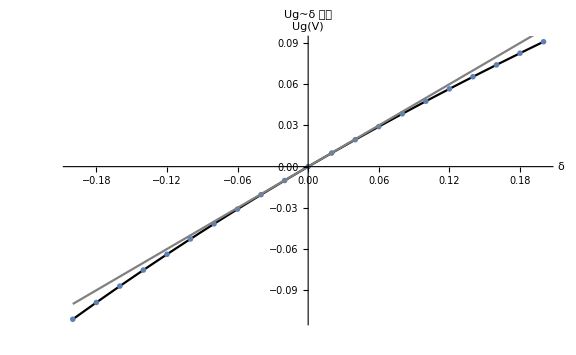

0.505

InterpolatingFunction[…][x]

2525.

```mathematica
r0 = 5000;
r1 = r2 = r0;
r3 = 4999.18;
r4 = Range[4000,6000,100];
ug = {-111.12,-98.91,-86.96,-75.28,-63.83,-52.64,-41.67,-30.93,-20.41,-10.10,0,9.90,19.61,29.13,38.46,47.62,56.61,65.43,74.08,82.58,90.92} * 10^-3;
deltar = r4 - r0;
ith = deltar / r0;

data1 = Transpose[{ith, ug}];
data2y[x_] := us * x / 4;
grah = Interpolation[data1,InterpolationOrder->1];

FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,-0.2}]
FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,0.2}]
tmpx = 0.10461538461538444;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];
tmpx = -0.09489361702127669;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];

Show[Plot[grah[x],{x,Min[ith],Max[ith]},PlotStyle->Black],
ListPlot[data1,PlotMarkers->Style["x",10]],
Plot[data2y[x], {x,Min[ith],Max[ith]},PlotStyle->Gray],
AxesLabel->{Style["δ",10], Style["Ug(V)",9]},
PlotLabel->Style["Ug~δ 曲线",25,FontFamily->"Hack",Bold,FontColor->Black],
ImageSize->Large]
D[grah[x],x]/.x->0
D[grah[x],x]
D[grah[x] * r0,x]/.x->0
```